```mathematica
<<xlr8r.m;
<<Cellzilla2D.m;
$HistoryLength=5;
```

xCellerator 0.95 (28-Feb-2014) loaded Thu 8 Jun 2017 21:18:21
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (3.0.51c (08 June 2017)) loaded Thu 8 Jun 2017 21:18:21
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

## Define a template with two cells

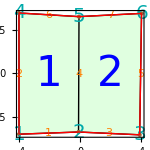

```mathematica
q=RandomizeTemplate[TemplateRectangular[{-4,4, 4},{-2, 2, 4}],.05];
Q=Tissue2DTissue[q];
ShowTissue[Q, "CellNumbers"-> True, "EdgeNumbers"-> True,
"CellNumberStyle"-> {Blue,42}, "BoundaryStyle"-> Red,
"EdgeNumberStyle"-> Orange,"Vertices"-> {Brown,PointSize[.02]},
"Nucleus"-> False, "VertexNumbers"-> True,"VertexNumberStyle"-> {20,Darker[Cyan]},
Frame-> True,BaseStyle-> {FontSize-> 17}, ImageSize-> 150]
```

## Define the network and the network parameters

```mathematica
network={{A⇄∅,kA, dA}, {pee⇄∅, kP,dP}};
diff={{A, βout, βin, βw}};
pumps={{pee, Fout, Fin}};
parameters={dA->0.1,kA->.1,kP-> .1, dP-> .1, halfwall->.025,DA->700,k->10,μ->1,P->1.5, Fout-> 1, Fin-> 1, βin-> 1, βout-> 1, βw-> 1};
wall={{A-> ∅, kA}};
```

## Run the simulation

simdir = /Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/Snapshot0001.png

Actual Clock Time:  | 09-Jun-2017-at-12:27:08
Memory in Use (GB):  | 0.329455
Max Memory Used (GB):  | 0.34371
Free Memory (GB):  | 0.185055

L1 Anticlinal division:Cell 2

Cell 2 (static cell 2) divides at t = 1.12583

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/Snapshot0002.png

Actual Clock Time:  | 09-Jun-2017-at-12:27:10
Memory in Use (GB):  | 0.328775
Max Memory Used (GB):  | 0.34371
Free Memory (GB):  | 0.218716
CPU Used(seconds):  | 1.11575
Number of Cells:  | 3
Cell Divisions:  | 1
Simulator Steps:  | 2
Number of Variables:  | 67

L1 Anticlinal division:Cell 1

Cell 1 (static cell 1) divides at t = 1.53687

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/Snapshot0003.png

Actual Clock Time:  | 09-Jun-2017-at-12:27:11
Memory in Use (GB):  | 0.32982
Max Memory Used (GB):  | 0.34371
Free Memory (GB):  | 0.2155
CPU Used(seconds):  | 2.48767
Number of Cells:  | 4
Cell Divisions:  | 2
Simulator Steps:  | 3
Number of Variables:  | 97

L1 Anticlinal division:Cell 3

Cell 3 (static cell 3) divides at t = 3.26501

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/Snapshot0004.png

Actual Clock Time:  | 09-Jun-2017-at-12:27:12
Memory in Use (GB):  | 0.331042
Max Memory Used (GB):  | 0.34371
Free Memory (GB):  | 0.213829
CPU Used(seconds):  | 4.1863
Number of Cells:  | 5
Cell Divisions:  | 3
Simulator Steps:  | 4
Number of Variables:  | 127

L1 Anticlinal division:Cell 1

Cell 1 (static cell 1) divides at t = 3.56209

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/Snapshot0005.png

Actual Clock Time:  | 09-Jun-2017-at-12:27:14
Memory in Use (GB):  | 0.331867
Max Memory Used (GB):  | 0.34371
Free Memory (GB):  | 0.212646
CPU Used(seconds):  | 6.1151
Number of Cells:  | 6
Cell Divisions:  | 4
Simulator Steps:  | 5
Number of Variables:  | 157

L1 Anticlinal division:Cell 2

Cell 2 (static cell 2) divides at t = 3.80503

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/Snapshot0006.png

Actual Clock Time:  | 09-Jun-2017-at-12:27:16
Memory in Use (GB):  | 0.333558
Max Memory Used (GB):  | 0.34371
Free Memory (GB):  | 0.21101
CPU Used(seconds):  | 8.30434
Number of Cells:  | 7
Cell Divisions:  | 5
Simulator Steps:  | 6
Number of Variables:  | 187

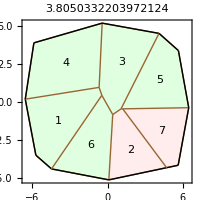

Simulation Completed at t = 3.80503 after 5 cell divisions; Normal Exit. CPU: 8.33108

```mathematica
SIM=grow[Q,0,10,
"Debug"-> False, 
"NDebug"-> False,
"Walls"-> True, 
"TestCase"-> "test", 
"SaveODES"-> True,
"SaveEquations"-> True, 
"MaxDivisions"-> 5, 
"Reactions"-> network, 
"Pumps"-> pumps,
"Diffusion"-> diff, 
"WallReactions"->wall,
 "BoundaryConditions"-> {A-> .1}, 
"Growing"-> True,
"Weights"-> {1,1,0,0},  
"Parameters"-> parameters, 
"DivisionThreshold"-> 25, 
"Verbose"-> False];
```

## Examine the simulation folder

```mathematica
$SIMDIR
```

/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227

```mathematica
Short[ShowSavedFiles[], 5]
```

{/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/DTissue0001.nb,«33»,/Users/mat…imeSpans.nb}

```mathematica
ShowSavedFiles["ODE"]
```

{/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/ODES0001.nb,/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/ODES0002.nb,/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/ODES0003.nb,/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/ODES0004.nb,/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/ODES0005.nb}

```mathematica
Short[GetSavedFile[$SIMDIR, "Net",1], 5]
```

/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/Network0001.nb

{{A[1]→∅,kA},{∅→A[1],dA},«109»,{∅→x[6],-0.5 P (y[3][t]-y[5][t])},{∅→y[6],-0.5 P (-x[3][t]+x[5][t])}}

```mathematica
GetSavedFile[$SIMDIR, "Options",1]
```

/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/Simulation-Options.nb

{Reactions→{{A⇄∅,kA,dA},{pee⇄∅,kP,dP}},Diffusion→{{A,βout,βin,βw}},Pumps→{{pee,Fout,Fin}},Intercellular→{},k→k,mu→μ,P→P,DivisionModel→Errera,DivisionThreshold→25,DivisionSigma→0.1,DivisionVariable→cell,Weights→{1,1,1},Debug→False,NDebug→False,Walls→True,TestCase→test,SaveODES→True,SaveEquations→True,MaxDivisions→5,WallReactions→{{A→∅,kA}},BoundaryConditions→{A→0.1},Growing→True,Weights→{1,1,0,0},Parameters→{dA→0.1,kA→0.1,kP→0.1,dP→0.1,halfwall→0.025,DA→700,k→10,μ→1,P→1.5,Fout→1,Fin→1,βin→1,βout→1,βw→1},DivisionThreshold→25,Verbose→False}

```mathematica
GetSavedFile[$SIMDIR, "IC",1]
```

/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/IC0001.nb

{DivisionEventFlag→-0.25,CellDivisionThreshold[1]→27.57,CellDivisionThreshold[2]→23.75,A[1]→0.00970552,A[2]→0.03914,A[1,1]→0.0110059,A[1,2]→0.00384749,A[1,4]→0.00978369,A[1,6]→0.0409925,A[2,3]→0.0103813,A[2,4]→0.0382252,A[2,5]→0.0257912,A[2,7]→0.0383324,pee[1]→0.0482946,pee[2]→0.0335223,pee[1,1]→0.0284928,pee[1,2]→0.0367343,pee[1,4]→0.000977137,pee[1,6]→0.0204268,pee[2,3]→0.0474946,pee[2,4]→0.0168368,pee[2,5]→0.0368499,pee[2,7]→0.0356861,x[1]→-3.99811,x[2]→-0.110829,x[3]→3.88398,x[4]→-4.00339,x[5]→-0.080504,x[6]→4.00601,y[1]→-2.09546,y[2]→-2.02054,y[3]→-2.11727,y[4]→2.08714,y[5]→1.96128,y[6]→2.07323,cell[1]→15.9417,cell[2]→16.5102,tip[1]→-4.00339,tip[2]→2.08714,ell[1]→3.888,ell[2]→4.1826,ell[3]→3.99598,ell[4]→3.98194,ell[5]→4.19227,ell[6]→3.9249,ell[7]→4.08805,ellX[1]→-3.88728,ellX[2]→0.00527689,ellX[3]→-3.99481,ellX[4]→-0.0303247,ellX[5]→-0.122035,ellX[6]→-3.92288,ellX[7]→-4.08652,ellY[1]→-0.0749186,ellY[2]→-4.1826,ellY[3]→0.0967214,ellY[4]→-3.98182,ellY[5]→-4.1905,ellY[6]→0.125861,ellY[7]→-0.111957,resting[1]→3.888,resting[2]→4.1826,resting[3]→3.99598,resting[4]→3.98194,resting[5]→4.19227,resting[6]→3.9249,resting[7]→4.08805}

```mathematica
GetSavedFile[$SIMDIR, "Lineage",1]
```

/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/Lineage.nb

{0→1,0→2,2→3,1→4,3→5,1→6,2→7}

```mathematica
GetSavedFile[$SIMDIR, "Net",1]
```

/Users/mathman/Cellzilla/Simulations-09-Jun-17/test-09Jun17-1227/Network0001.nb

{{A[1]→∅,kA},{∅→A[1],dA},{pee[1]→∅,kP},{∅→pee[1],dP},{A[2]→∅,kA},{∅→A[2],dA},{pee[2]→∅,kP},{∅→pee[2],dP},{A[1]⇄∅,(βout ell[4][t])/(cell[1][t]),(βin A[1,4][t] ell[4][t])/(cell[1][t])},{A[1,4]⇄∅,βin/halfwall,(βout A[1][t])/halfwall},{A[2]⇄∅,(βout ell[4][t])/(cell[2][t]),(βin A[2,4][t] ell[4][t])/(cell[2][t])},{A[2,4]⇄∅,βin/halfwall,(βout A[2][t])/halfwall},{A[1,4]⇄∅,βw/halfwall,(βw A[2,4][t])/halfwall},{A[2,4]⇄∅,βw/halfwall,(βw A[1,4][t])/halfwall},{A[1,1]⇄∅,(1.41421 βw)/(ell[1][t] √(1.-((x[1][t]-x[2][t]) (x[1][t]-x[4][t]))/(ell[1][t] ell[2][t])-((y[1][t]-y[2][t]) (y[1][t]-y[4][t]))/(ell[1][t] ell[2][t]))),(1.41421 βw A[1,1][t])/(ell[1][t] √(1.-((x[1][t]-x[2][t]) (x[1][t]-x[4][t]))/(ell[1][t] ell[2][t])-((y[1][t]-y[2][t]) (y[1][t]-y[4][t]))/(ell[1][t] ell[2][t])))},{A[1,2]⇄∅,(1.41421 βw)/(ell[2][t] √(1.-((x[1][t]-x[2][t]) (x[1][t]-x[4][t]))/(ell[1][t] ell[2][t])-((y[1][t]-y[2][t]) (y[1][t]-y[4][t]))/(ell[1][t] ell[2][t]))),(1.41421 βw A[1,2][t])/(ell[2][t] √(1.-((x[1][t]-x[2][t]) (x[1][t]-x[4][t]))/(ell[1][t] ell[2][t])-((y[1][t]-y[2][t]) (y[1][t]-y[4][t]))/(ell[1][t] ell[2][t])))},{A[1,1]⇄∅,(1.41421 βw)/(ell[1][t] √(1.+((x[1][t]-x[2][t]) (x[2][t]-x[5][t]))/(ell[1][t] ell[4][t])+((y[1][t]-y[2][t]) (y[2][t]-y[5][t]))/(ell[1][t] ell[4][t]))),(1.41421 βw A[1,1][t])/(ell[1][t] √(1.+((x[1][t]-x[2][t]) (x[2][t]-x[5][t]))/(ell[1][t] ell[4][t])+((y[1][t]-y[2][t]) (y[2][t]-y[5][t]))/(ell[1][t] ell[4][t])))},{A[1,4]⇄∅,(1.41421 βw)/(ell[4][t] √(1.+((x[1][t]-x[2][t]) (x[2][t]-x[5][t]))/(ell[1][t] ell[4][t])+((y[1][t]-y[2][t]) (y[2][t]-y[5][t]))/(ell[1][t] ell[4][t]))),(1.41421 βw A[1,4][t])/(ell[4][t] √(1.+((x[1][t]-x[2][t]) (x[2][t]-x[5][t]))/(ell[1][t] ell[4][t])+((y[1][t]-y[2][t]) (y[2][t]-y[5][t]))/(ell[1][t] ell[4][t])))},{A[1,2]⇄∅,(1.41421 βw)/(ell[2][t] √(1.+((x[1][t]-x[4][t]) (x[4][t]-x[5][t]))/(ell[2][t] ell[6][t])+((y[1][t]-y[4][t]) (y[4][t]-y[5][t]))/(ell[2][t] ell[6][t]))),(1.41421 βw A[1,2][t])/(ell[2][t] √(1.+((x[1][t]-x[4][t]) (x[4][t]-x[5][t]))/(ell[2][t] ell[6][t])+((y[1][t]-y[4][t]) (y[4][t]-y[5][t]))/(ell[2][t] ell[6][t])))},{A[1,6]⇄∅,(1.41421 βw)/(ell[6][t] √(1.+((x[1][t]-x[4][t]) (x[4][t]-x[5][t]))/(ell[2][t] ell[6][t])+((y[1][t]-y[4][t]) (y[4][t]-y[5][t]))/(ell[2][t] ell[6][t]))),(1.41421 βw A[1,6][t])/(ell[6][t] √(1.+((x[1][t]-x[4][t]) (x[4][t]-x[5][t]))/(ell[2][t] ell[6][t])+((y[1][t]-y[4][t]) (y[4][t]-y[5][t]))/(ell[2][t] ell[6][t])))},{A[2,3]⇄∅,(1.41421 βw)/(ell[3][t] √(1.-((x[2][t]-x[3][t]) (x[2][t]-x[5][t]))/(ell[3][t] ell[4][t])-((y[2][t]-y[3][t]) (y[2][t]-y[5][t]))/(ell[3][t] ell[4][t]))),(1.41421 βw A[2,3][t])/(ell[3][t] √(1.-((x[2][t]-x[3][t]) (x[2][t]-x[5][t]))/(ell[3][t] ell[4][t])-((y[2][t]-y[3][t]) (y[2][t]-y[5][t]))/(ell[3][t] ell[4][t])))},{A[2,4]⇄∅,(1.41421 βw)/(ell[4][t] √(1.-((x[2][t]-x[3][t]) (x[2][t]-x[5][t]))/(ell[3][t] ell[4][t])-((y[2][t]-y[3][t]) (y[2][t]-y[5][t]))/(ell[3][t] ell[4][t]))),(1.41421 βw A[2,4][t])/(ell[4][t] √(1.-((x[2][t]-x[3][t]) (x[2][t]-x[5][t]))/(ell[3][t] ell[4][t])-((y[2][t]-y[3][t]) (y[2][t]-y[5][t]))/(ell[3][t] ell[4][t])))},{A[2,3]⇄∅,(1.41421 βw)/(ell[3][t] √(1.+((x[2][t]-x[3][t]) (x[3][t]-x[6][t]))/(ell[3][t] ell[5][t])+((y[2][t]-y[3][t]) (y[3][t]-y[6][t]))/(ell[3][t] ell[5][t]))),(1.41421 βw A[2,3][t])/(ell[3][t] √(1.+((x[2][t]-x[3][t]) (x[3][t]-x[6][t]))/(ell[3][t] ell[5][t])+((y[2][t]-y[3][t]) (y[3][t]-y[6][t]))/(ell[3][t] ell[5][t])))},{A[2,5]⇄∅,(1.41421 βw)/(ell[5][t] √(1.+((x[2][t]-x[3][t]) (x[3][t]-x[6][t]))/(ell[3][t] ell[5][t])+((y[2][t]-y[3][t]) (y[3][t]-y[6][t]))/(ell[3][t] ell[5][t]))),(1.41421 βw A[2,5][t])/(ell[5][t] √(1.+((x[2][t]-x[3][t]) (x[3][t]-x[6][t]))/(ell[3][t] ell[5][t])+((y[2][t]-y[3][t]) (y[3][t]-y[6][t]))/(ell[3][t] ell[5][t])))},{A[1,4]⇄∅,(1.41421 βw)/(ell[4][t] √(1.-((x[2][t]-x[5][t]) (x[4][t]-x[5][t]))/(ell[4][t] ell[6][t])-((y[2][t]-y[5][t]) (y[4][t]-y[5][t]))/(ell[4][t] ell[6][t]))),(1.41421 βw A[1,4][t])/(ell[4][t] √(1.-((x[2][t]-x[5][t]) (x[4][t]-x[5][t]))/(ell[4][t] ell[6][t])-((y[2][t]-y[5][t]) (y[4][t]-y[5][t]))/(ell[4][t] ell[6][t])))},{A[1,6]⇄∅,(1.41421 βw)/(ell[6][t] √(1.-((x[2][t]-x[5][t]) (x[4][t]-x[5][t]))/(ell[4][t] ell[6][t])-((y[2][t]-y[5][t]) (y[4][t]-y[5][t]))/(ell[4][t] ell[6][t]))),(1.41421 βw A[1,6][t])/(ell[6][t] √(1.-((x[2][t]-x[5][t]) (x[4][t]-x[5][t]))/(ell[4][t] ell[6][t])-((y[2][t]-y[5][t]) (y[4][t]-y[5][t]))/(ell[4][t] ell[6][t])))},{A[2,4]⇄∅,(1.41421 βw)/(ell[4][t] √(1.+((x[2][t]-x[5][t]) (x[5][t]-x[6][t]))/(ell[4][t] ell[7][t])+((y[2][t]-y[5][t]) (y[5][t]-y[6][t]))/(ell[4][t] ell[7][t]))),(1.41421 βw A[2,4][t])/(ell[4][t] √(1.+((x[2][t]-x[5][t]) (x[5][t]-x[6][t]))/(ell[4][t] ell[7][t])+((y[2][t]-y[5][t]) (y[5][t]-y[6][t]))/(ell[4][t] ell[7][t])))},{A[2,7]⇄∅,(1.41421 βw)/(ell[7][t] √(1.+((x[2][t]-x[5][t]) (x[5][t]-x[6][t]))/(ell[4][t] ell[7][t])+((y[2][t]-y[5][t]) (y[5][t]-y[6][t]))/(ell[4][t] ell[7][t]))),(1.41421 βw A[2,7][t])/(ell[7][t] √(1.+((x[2][t]-x[5][t]) (x[5][t]-x[6][t]))/(ell[4][t] ell[7][t])+((y[2][t]-y[5][t]) (y[5][t]-y[6][t]))/(ell[4][t] ell[7][t])))},{A[2,5]⇄∅,(1.41421 βw)/(ell[5][t] √(1.-((x[3][t]-x[6][t]) (x[5][t]-x[6][t]))/(ell[5][t] ell[7][t])-((y[3][t]-y[6][t]) (y[5][t]-y[6][t]))/(ell[5][t] ell[7][t]))),(1.41421 βw A[2,5][t])/(ell[5][t] √(1.-((x[3][t]-x[6][t]) (x[5][t]-x[6][t]))/(ell[5][t] ell[7][t])-((y[3][t]-y[6][t]) (y[5][t]-y[6][t]))/(ell[5][t] ell[7][t])))},{A[2,7]⇄∅,(1.41421 βw)/(ell[7][t] √(1.-((x[3][t]-x[6][t]) (x[5][t]-x[6][t]))/(ell[5][t] ell[7][t])-((y[3][t]-y[6][t]) (y[5][t]-y[6][t]))/(ell[5][t] ell[7][t]))),(1.41421 βw A[2,7][t])/(ell[7][t] √(1.-((x[3][t]-x[6][t]) (x[5][t]-x[6][t]))/(ell[5][t] ell[7][t])-((y[3][t]-y[6][t]) (y[5][t]-y[6][t]))/(ell[5][t] ell[7][t])))},{A[1]⇄∅,(βout ell[1][t])/(cell[1][t]),(βin A[1,1][t] ell[1][t])/(cell[1][t])},{A[1,1]⇄∅,βin/halfwall,(βout A[1][t])/halfwall},{A[1]⇄∅,(βout ell[2][t])/(cell[1][t]),(βin A[1,2][t] ell[2][t])/(cell[1][t])},{A[1,2]⇄∅,βin/halfwall,(βout A[1][t])/halfwall},{A[1]⇄∅,(βout ell[6][t])/(cell[1][t]),(βin A[1,6][t] ell[6][t])/(cell[1][t])},{A[1,6]⇄∅,βin/halfwall,(βout A[1][t])/halfwall},{A[2]⇄∅,(βout ell[3][t])/(cell[2][t]),(βin A[2,3][t] ell[3][t])/(cell[2][t])},{A[2,3]⇄∅,βin/halfwall,(βout A[2][t])/halfwall},{A[2]⇄∅,(βout ell[5][t])/(cell[2][t]),(βin A[2,5][t] ell[5][t])/(cell[2][t])},{A[2,5]⇄∅,βin/halfwall,(βout A[2][t])/halfwall},{A[2]⇄∅,(βout ell[7][t])/(cell[2][t]),(βin A[2,7][t] ell[7][t])/(cell[2][t])},{A[2,7]⇄∅,βin/halfwall,(βout A[2][t])/halfwall},{pee[1]⇒∅,(Fout ell[4][t])/(cell[1][t])},{∅⇒pee[1,4],(Fout ell[4][t])/(cell[1][t])},{pee[1,4]⇒∅,(Fin ell[4][t])/(cell[1][t])},{∅⇒pee[1],(Fin ell[4][t])/(cell[1][t])},{pee[2]⇒∅,(Fout ell[4][t])/(cell[2][t])},{∅⇒pee[2,4],(Fout ell[4][t])/(cell[2][t])},{pee[2,4]⇒∅,(Fin ell[4][t])/(cell[2][t])},{∅⇒pee[2],(Fin ell[4][t])/(cell[2][t])},{pee[1]⇒∅,(Fout ell[1][t])/(cell[1][t])},{∅⇒pee[1,1],(Fout ell[1][t])/(cell[1][t])},{pee[1,1]⇒∅,(Fin ell[1][t])/(cell[1][t])},{∅⇒pee[1],(Fin ell[1][t])/(cell[1][t])},{pee[1]⇒∅,(Fout ell[2][t])/(cell[1][t])},{∅⇒pee[1,2],(Fout ell[2][t])/(cell[1][t])},{pee[1,2]⇒∅,(Fin ell[2][t])/(cell[1][t])},{∅⇒pee[1],(Fin ell[2][t])/(cell[1][t])},{pee[1]⇒∅,(Fout ell[6][t])/(cell[1][t])},{∅⇒pee[1,6],(Fout ell[6][t])/(cell[1][t])},{pee[1,6]⇒∅,(Fin ell[6][t])/(cell[1][t])},{∅⇒pee[1],(Fin ell[6][t])/(cell[1][t])},{pee[2]⇒∅,(Fout ell[3][t])/(cell[2][t])},{∅⇒pee[2,3],(Fout ell[3][t])/(cell[2][t])},{pee[2,3]⇒∅,(Fin ell[3][t])/(cell[2][t])},{∅⇒pee[2],(Fin ell[3][t])/(cell[2][t])},{pee[2]⇒∅,(Fout ell[5][t])/(cell[2][t])},{∅⇒pee[2,5],(Fout ell[5][t])/(cell[2][t])},{pee[2,5]⇒∅,(Fin ell[5][t])/(cell[2][t])},{∅⇒pee[2],(Fin ell[5][t])/(cell[2][t])},{pee[2]⇒∅,(Fout ell[7][t])/(cell[2][t])},{∅⇒pee[2,7],(Fout ell[7][t])/(cell[2][t])},{pee[2,7]⇒∅,(Fin ell[7][t])/(cell[2][t])},{∅⇒pee[2],(Fin ell[7][t])/(cell[2][t])},{A[1,1]→∅,kA},{A[1,4]→∅,kA},{A[1,6]→∅,kA},{A[1,2]→∅,kA},{A[2,3]→∅,kA},{A[2,5]→∅,kA},{A[2,7]→∅,kA},{A[2,4]→∅,kA},{∅→resting[1],1/2 μ (Abs[ell[1][t]-resting[1][t]]+ell[1][t]-resting[1][t])},{∅→resting[2],1/2 μ (Abs[ell[2][t]-resting[2][t]]+ell[2][t]-resting[2][t])},{∅→resting[3],1/2 μ (Abs[ell[3][t]-resting[3][t]]+ell[3][t]-resting[3][t])},{∅→resting[4],1/2 μ (Abs[ell[4][t]-resting[4][t]]+ell[4][t]-resting[4][t])},{∅→resting[5],1/2 μ (Abs[ell[5][t]-resting[5][t]]+ell[5][t]-resting[5][t])},{∅→resting[6],1/2 μ (Abs[ell[6][t]-resting[6][t]]+ell[6][t]-resting[6][t])},{∅→resting[7],1/2 μ (Abs[ell[7][t]-resting[7][t]]+ell[7][t]-resting[7][t])},{∅→x[1],k (1-(resting[1][t])/(ell[1][t])) (-x[1][t]+x[2][t])+k (1-(resting[2][t])/(ell[2][t])) (-x[1][t]+x[4][t])},{∅→y[1],k (1-(resting[1][t])/(ell[1][t])) (-y[1][t]+y[2][t])+k (1-(resting[2][t])/(ell[2][t])) (-y[1][t]+y[4][t])},{∅→x[2],k (1-(resting[1][t])/(ell[1][t])) (x[1][t]-x[2][t])+k (1-(resting[3][t])/(ell[3][t])) (-x[2][t]+x[3][t])+k (1-(resting[4][t])/(ell[4][t])) (-x[2][t]+x[5][t])},{∅→y[2],k (1-(resting[1][t])/(ell[1][t])) (y[1][t]-y[2][t])+k (1-(resting[3][t])/(ell[3][t])) (-y[2][t]+y[3][t])+k (1-(resting[4][t])/(ell[4][t])) (-y[2][t]+y[5][t])},{∅→x[3],k (1-(resting[3][t])/(ell[3][t])) (x[2][t]-x[3][t])+k (1-(resting[5][t])/(ell[5][t])) (-x[3][t]+x[6][t])},{∅→y[3],k (1-(resting[3][t])/(ell[3][t])) (y[2][t]-y[3][t])+k (1-(resting[5][t])/(ell[5][t])) (-y[3][t]+y[6][t])},{∅→x[4],k (1-(resting[2][t])/(ell[2][t])) (x[1][t]-x[4][t])+k (1-(resting[6][t])/(ell[6][t])) (-x[4][t]+x[5][t])},{∅→y[4],k (1-(resting[2][t])/(ell[2][t])) (y[1][t]-y[4][t])+k (1-(resting[6][t])/(ell[6][t])) (-y[4][t]+y[5][t])},{∅→x[5],k (1-(resting[4][t])/(ell[4][t])) (x[2][t]-x[5][t])+k (1-(resting[6][t])/(ell[6][t])) (x[4][t]-x[5][t])+k (1-(resting[7][t])/(ell[7][t])) (-x[5][t]+x[6][t])},{∅→y[5],k (1-(resting[4][t])/(ell[4][t])) (y[2][t]-y[5][t])+k (1-(resting[6][t])/(ell[6][t])) (y[4][t]-y[5][t])+k (1-(resting[7][t])/(ell[7][t])) (-y[5][t]+y[6][t])},{∅→x[6],k (1-(resting[5][t])/(ell[5][t])) (x[3][t]-x[6][t])+k (1-(resting[7][t])/(ell[7][t])) (x[5][t]-x[6][t])},{∅→y[6],k (1-(resting[5][t])/(ell[5][t])) (y[3][t]-y[6][t])+k (1-(resting[7][t])/(ell[7][t])) (y[5][t]-y[6][t])},{∅→x[1],0.5 P (y[2][t]-y[4][t])},{∅→y[1],0.5 P (-x[2][t]+x[4][t])},{∅→x[2],-0.5 P (y[1][t]-y[3][t])},{∅→y[2],-0.5 P (-x[1][t]+x[3][t])},{∅→x[3],-0.5 P (y[2][t]-y[6][t])},{∅→y[3],-0.5 P (-x[2][t]+x[6][t])},{∅→x[4],0.5 P (y[1][t]-y[5][t])},{∅→y[4],0.5 P (-x[1][t]+x[5][t])},{∅→x[5],0.5 P (y[4][t]-y[6][t])},{∅→y[5],0.5 P (-x[4][t]+x[6][t])},{∅→x[6],-0.5 P (y[3][t]-y[5][t])},{∅→y[6],-0.5 P (-x[3][t]+x[5][t])}}